## Cameron Embree - Assignment 4

### Work in Progress...

Assignment 3: Working with Graphics

The format of the legislator files is:

 1.  Congress Number
 2.  ICPSR ID Number:  5 digit code assigned by the ICPSR as 
                       corrected by Howard Rosenthal and myself.
 3.  State Code:  2 digit ICPSR State Code.
 4.  Congressional District Number (0 if Senate)
 5.  State Name
 6.  Party Code:  100 = Dem., 200 = Repub. (See PARTY3.DAT for a full set of codes of minor and historical parties)
 7.  Name
 8.  1st Dimension Coordinate
 9.  2nd Dimension Coordinate
10.  1st Dimension Bootstrapped Standard Error
11.  2nd Dimension Bootstrapped Standard Error
12.  Correlation Between 1st and 2nd Dimension Bootstrapped Estimates over the 1000 trials (for computing the ellipsoid of estimated points)
13.  Log-Likelihood
14.  Number of Votes
15.  Number of Classification Errors
16.  Geometric Mean Probability

```mathematica
SetDirectory[NotebookDirectory[]];
congdata=Import["HL01112D21_PRES_BSSE.csv"]
```

{{1,9062,1,98,CONNECT,5000,STURGES,0.637,0.327,0.115,0.101,0.113,-26.9513,80,12,0.714},{1,9706,1,98,CONNECT,5000,WADSWORTH,0.749,0.134,0.089,0.1,-0.238,-18.328,86,5,0.808},«37073»,{112,21190,25,8,WISCONS,200,RIBBLE,0.886,-0.193,0.187,0.141,-0.077,-265.329,1412,113,0.829},{112,20953,68,1,WYOMING,200,LUMMIS,0.932,-0.211,0.197,0.144,-0.187,-279.545,1395,117,0.818}}

```mathematica
(* 1. Create a function that takes a legislator and outputs a Point with the coordinates for that legislator.Plot a few legislators using this function and the Graphics command. *)
```

```mathematica
getPointForName[name_String]:=Block[{},
x=Select[congdata,(#[[7]]==name)&];
y=x[[1]];
Point[y[[8;;9]]]
]

(* TEST *)

somePoints=List[getPointForName["WADSWORTH"],
getPointForName["KIND"],
getPointForName["RIBBLE"],
getPointForName["SENSENBR"]
]

Graphics[somePoints]
InputForm[Graphics[somePoints]];
```

{Point[{0.749,0.134}],Point[{-0.265,-0.181}],Point[{0.886,-0.193}],Point[{1.014,-0.472}]}

-Graphics-

```mathematica
(* 2. Create a function that takes in a legislator and outputs a point with color red or blue de-pending on the party of the legislator. Plot a few legislators using this function and the Graphics command. Figure out a way to deal with early congresses where they were not just republicans and democrats.*)
```

```mathematica
getColoredPointForName[name_String]:=Block[{},
x=Select[congdata,(#[[7]]==name)&];
y=x[[1]];
color=If[y[[6]]==100,Red,Blue,Black];
point=Point[y[[8;;9]]];
List[color,point]
]

(* TEST *)
somePoints=List[getColoredPointForName["WADSWORTH"],
getColoredPointForName["KIND"],
getColoredPointForName["RIBBLE"],
getColoredPointForName["SENSENBR"]
]

Graphics[somePoints]
InputForm[Graphics[somePoints]]
```

{{RGBColor[0,0,1],Point[{0.749,0.134}]},{RGBColor[1,0,0],Point[{-0.265,-0.181}]},{RGBColor[0,0,1],Point[{0.886,-0.193}]},{RGBColor[0,0,1],Point[{1.014,-0.472}]}}

-Graphics-

Graphics[{{RGBColor[0, 0, 1], Point[{0.749, 0.134}]}, {RGBColor[1, 0, 0], Point[{-0.265, -0.181}]}, 
  {RGBColor[0, 0, 1], Point[{0.886, -0.193}]}, {RGBColor[0, 0, 1], Point[{1.014, -0.472}]}}]

```mathematica
(* 3. Create a function that creates a triangle for a legislator colored red or blue if the legislator is from a certain state and outputs just a point if the legislator is not from a certain state. Plot a few legislators using this function and the Graphics command. *)
```

```mathematica
tri[{x_,y_},s_]:=Polygon[Table[{s*Cos[i]+x,s*Sin[i]+y},{i,-Pi/6,7Pi/6,2Pi/3}]]

marker[x_]:=If[x[[1]]=="dog",tri[x[[2]],.01],Point[x[[2]]]]

getColoredPointForName[name_String]:=Block[{},
x=Select[congdata,(#[[7]]==name)&];
y=x[[1]];
color=If[y[[6]]==100,Red,Blue,Black];
poly=tri[y[[8;;9]],.01];

List[color,poly]
]

(* TEST *)
somePoints=List[getColoredPointForName["WADSWORTH"],
getColoredPointForName["KIND"],
getColoredPointForName["RIBBLE"],
getColoredPointForName["SENSENBR"]
]

Graphics[somePoints]
InputForm[Graphics[somePoints]]
```

{{RGBColor[0,0,1],Polygon[{{0.75766,0.129},{0.749,0.144},{0.74034,0.129}}]},{RGBColor[1,0,0],Polygon[{{-0.25634,-0.186},{-0.265,-0.171},{-0.27366,-0.186}}]},{RGBColor[0,0,1],Polygon[{{0.89466,-0.198},{0.886,-0.183},{0.87734,-0.198}}]},{RGBColor[0,0,1],Polygon[{{1.02266,-0.477},{1.014,-0.462},{1.00534,-0.477}}]}}

-Graphics-

Graphics[{{RGBColor[0, 0, 1], Polygon[{{0.7576602540378444, 0.129}, {0.749, 0.14400000000000002}, 
     {0.7403397459621556, 0.129}}]}, {RGBColor[1, 0, 0], 
   Polygon[{{-0.25633974596215564, -0.186}, {-0.265, -0.17099999999999999}, {-0.2736602540378444, -0.186}}]}, 
  {RGBColor[0, 0, 1], Polygon[{{0.8946602540378444, -0.198}, {0.886, -0.183}, {0.8773397459621556, -0.198}}]}, 
  {RGBColor[0, 0, 1], Polygon[{{1.0226602540378444, -0.477}, {1.014, -0.46199999999999997}, {1.0053397459621556, -0.477}}]}}]

```mathematica
(* 4. Modify your above work with Tooltip so that the legislators name and state appear when you mouseover the point or triangle.*)
```

```mathematica
tri[{x_,y_},s_]:=Polygon[Table[{s*Cos[i]+x,s*Sin[i]+y},{i,-Pi/6,7Pi/6,2Pi/3}]]

marker[x_]:=If[x[[1]]=="dog",tri[x[[2]],.01],Point[x[[2]]]]

getColoredPointForName[name_String]:=Block[{},
x=Select[congdata,(#[[7]]==name)&];
y=x[[1]];
color=If[y[[6]]==100,Red,Blue,Black];
poly=tri[y[[8;;9]],.02];

Tooltip[List[color,poly],name]
]

(* TEST *)
somePoints=List[getColoredPointForName["WADSWORTH"],
getColoredPointForName["KIND"],
getColoredPointForName["RIBBLE"],
getColoredPointForName["SENSENBR"]
]

Graphics[somePoints]
InputForm[Graphics[somePoints]]
```

{{RGBColor[0,0,1],Polygon[{{0.766321,0.124},{0.749,0.154},{0.731679,0.124}}]},{RGBColor[1,0,0],Polygon[{{-0.247679,-0.191},{-0.265,-0.161},{-0.282321,-0.191}}]},{RGBColor[0,0,1],Polygon[{{0.903321,-0.203},{0.886,-0.173},{0.868679,-0.203}}]},{RGBColor[0,0,1],Polygon[{{1.03132,-0.482},{1.014,-0.452},{0.996679,-0.482}}]}}

-Graphics-

Graphics[{Tooltip[{RGBColor[0, 0, 1], Polygon[{{0.7663205080756887, 0.12400000000000001}, {0.749, 0.154}, 
      {0.7316794919243113, 0.12400000000000001}}]}, "WADSWORTH"], 
  Tooltip[{RGBColor[1, 0, 0], Polygon[{{-0.24767949192431124, -0.191}, {-0.265, -0.161}, {-0.28232050807568876, -0.191}}]}, 
   "KIND"], Tooltip[{RGBColor[0, 0, 1], Polygon[{{0.9033205080756888, -0.203}, {0.886, -0.17300000000000001}, 
      {0.8686794919243113, -0.203}}]}, "RIBBLE"], 
  Tooltip[{RGBColor[0, 0, 1], Polygon[{{1.0313205080756889, -0.482}, {1.014, -0.45199999999999996}, 
      {0.9966794919243113, -0.482}}]}, "SENSENBR"]}]

```mathematica
(* 5. Create code that allows you to choose a legislator and plot their points for their entire career in congress. *)
```

{{Point[{0.749,0.134}],Point[{0.749,0.134}],Point[{0.744,0.206}],Point[{0.728,0.166}],Point[{0.712,0.126}],Point[{0.697,0.086}],Point[{0.681,0.046}],Point[{0.665,0.006}],Point[{-0.116,-0.07}],Point[{-0.116,-0.07}],Point[{0.364,-0.641}],Point[{0.38,-0.643}],Point[{0.396,-0.645}],Point[{0.411,-0.647}],Point[{0.427,-0.649}],Point[{0.442,-0.651}],Point[{0.458,-0.653}],Point[{0.474,-0.655}],Point[{0.489,-0.656}],Point[{0.356,0.221}],Point[{0.346,0.205}],Point[{0.335,0.188}],Point[{0.324,0.172}],Point[{0.313,0.156}],Point[{0.302,0.139}],Point[{0.291,0.123}],Point[{0.28,0.106}],Point[{0.27,0.09}]}}

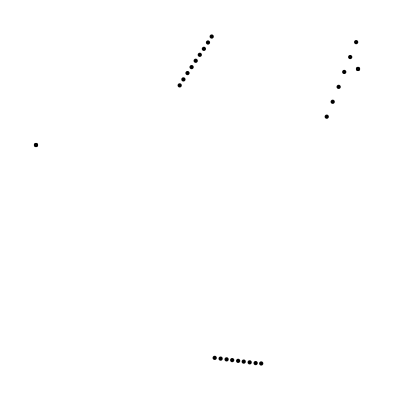

Graphics[{{Point[{0.749, 0.134}], Point[{0.749, 0.134}], Point[{0.744, 0.206}], Point[{0.728, 0.166}], Point[{0.712, 0.126}], 
   Point[{0.697, 0.086}], Point[{0.681, 0.046}], Point[{0.665, 0.006}], Point[{-0.116, -0.07}], Point[{-0.116, -0.07}], 
   Point[{0.364, -0.641}], Point[{0.38, -0.643}], Point[{0.396, -0.645}], Point[{0.411, -0.647}], Point[{0.427, -0.649}], 
   Point[{0.442, -0.651}], Point[{0.458, -0.653}], Point[{0.474, -0.655}], Point[{0.489, -0.656}], Point[{0.356, 0.221}], 
   Point[{0.346, 0.205}], Point[{0.335, 0.188}], Point[{0.324, 0.172}], Point[{0.313, 0.156}], Point[{0.302, 0.139}], 
   Point[{0.291, 0.123}], Point[{0.28, 0.106}], Point[{0.27, 0.09}]}}]

```mathematica
getPointForName[name_String]:=Block[{},
x=Select[congdata,(#[[7]]==name)&];
y=Map[#[[8;;9]]&,x];
Map[Point[#]&,y]
]

(* TEST *)
somePoints=List[getPointForName["WADSWORTH"]]

Graphics[somePoints]
InputForm[Graphics[somePoints]]
```

```mathematica
(* 6. Use the Dynamic environment to plot all legislators from a user selected congress,and have the members of a user selected state delegation be highlighted with a triangle. *)
```